```mathematica
Exit[]
```

#### Utilities & Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};
Comb5={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
Comb6={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"Palatino"],α Degree],Scaled[{x,y}]]
```

# QNMs of Halo Black Holes

```mathematica
(*Quit*)
```

```mathematica
(* non grid-based interpolation scheme to calculate QNMs of Schwarzschild black holes, I may have modified their method a bit. 
A HUGE CAUTION: any number you use has to be Rationalized or for large amount of grid points the code fail to work due to the differentiation matrices obtaining zero values*)
(* Main method taken from [arxiv:1610.08135v4] *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
n=15;
```

#### Differentiation matrices from built-in finite difference Mathematica functions

```mathematica
(*The above commented out code also calculates the differentiation matrices in the range we want but takes more time. It might be more accurate later when we deal with dirty black holes but for Schwarzschild the following method is enough.*)
min=0;
max=1;
 (*number of grid points used to discretize the metric components of spacetime, the compactified radial coordinate [0,1] and build the differentiation matrices*)
di=(max-min)/(n-1);(*equispaced data points*)
x=Table[i,{i,min,max,di}];
DF0=NDSolve`FiniteDifferenceDerivative[Derivative[0],Range[0,1,1/(n-1)],DifferenceOrder->n]["DifferentiationMatrix"] ;(*zeroth derivative*)
DF1=NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[0,1,1/(n-1)],DifferenceOrder->n-1]["DifferentiationMatrix"]; (*first derivative*)
DF2=NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[0,1,1/(n-1)],DifferenceOrder->n-2]["DifferentiationMatrix"]; (*second derivative*)
```

```mathematica
(* I delete the first and last entry in order to avoid calculating the functions at the extrema of the domain: 0 (rh) and 1 (∞), which are singular points *)
Delete[DF0,{{1},{n}}];
df0=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF1,{{1},{n}}];
df1=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF2,{{1},{n}}];
df2=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

## Finding modes

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;

ρmetric=background["HQ",M,a0,10^5][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=f'[rh];
derrmh=(D[ρprofile[r,M,a0,"HQ"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37367-0.08897056I,50];*)
FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];


sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

#### fundamental

```mathematica
l2n0Vac=δω[0,2,1000,SetPrecision[0.37-0.08I,50]];
```

```mathematica
l3n0Vac=δω[0,3,1000,SetPrecision[0.59-0.09I,50]];
```

```mathematica
l4n0Vac=δω[0,4,1000,SetPrecision[0.81-0.09I,50]];
```

```mathematica
l2n0=Monitor[Table[δω[10^compactness[[ii]],2,1000,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n0=Monitor[Table[δω[10^compactness[[ii]],3,1000,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n0=Monitor[Table[δω[10^compactness[[ii]],4,1000,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n0T=Join[{l2n0Vac},l2n0];
l3n0T=Join[{l3n0Vac},l3n0];
l4n0T=Join[{l4n0Vac},l4n0];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2R=Fit[datasetR[l2n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line3R=Fit[datasetR[l3n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line4R=Fit[datasetR[l4n0T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-5.8854761923652275378903585012070353671246102×10^-13+0.892535056034730804634065745891153727271085888 t-2.87586059681320725772044132245758330267343499 t^2

-2.3415135905529888271412951774644170122984052×10^-12+0.88137474982197990490227648866927701710637682 t+0.30399435379560894335139995984680104573184478 t^2

-1.43243658162052955868785132305612814743918804×10^-12+0.871447518582611679303401210184814996270844007 t+0.872065802227674835451611002975953768346780389 t^2

```mathematica
line2I=Fit[datasetI[l2n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line3I=Fit[datasetI[l3n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line4I=Fit[datasetI[l4n0T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-1.02345883632816681300164638133762987371277824×10^-11+1.10435964288194068591151869360347828993391227 t+7.10263444714026659395317924095492257299394272 t^2

5.145242072497785639572399998835840721923822×10^-13+0.93131582492649274196255463212214738828927524 t+12.3255412460861378867446215200098431563415 t^2

1.20231610846958815309538536090819152138380441×10^-11+0.911957000197864435282055135641774443072860149 t+6.80313636848082656184253131448629435195801054 t^2

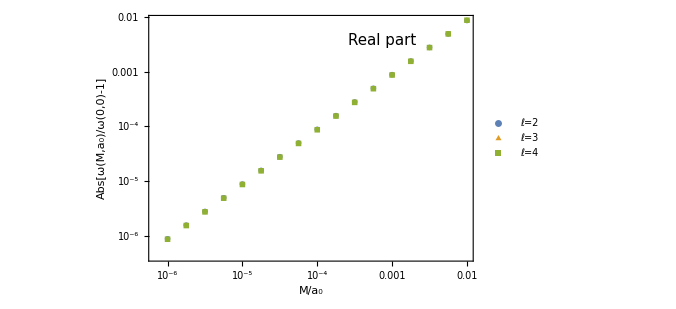

./plot/realZ_H_MM.pdf

```mathematica
p1=ListLogLogPlot[{
datasetR[l2n0T,10^-2],
datasetR[l3n0T,10^-2],
datasetR[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.72,0.9,Black]}]
Export["./plot/realZ_H_MM.pdf",%]
```

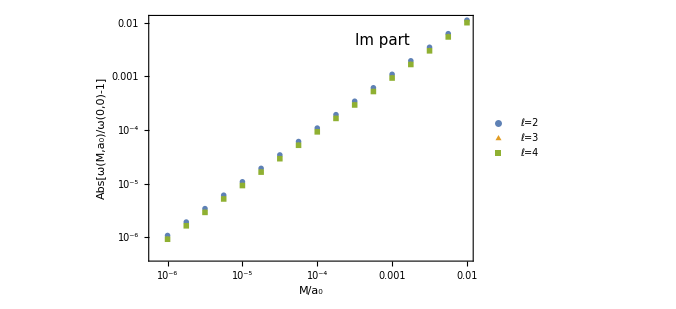

./plot/imZ_H_MM.pdf

```mathematica
p2=ListLogLogPlot[{
datasetI[l2n0T,10^-2],
datasetI[l3n0T,10^-2],
datasetI[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.72,0.9,Black]}]
Export["./plot/imZ_H_MM.pdf",%]
```

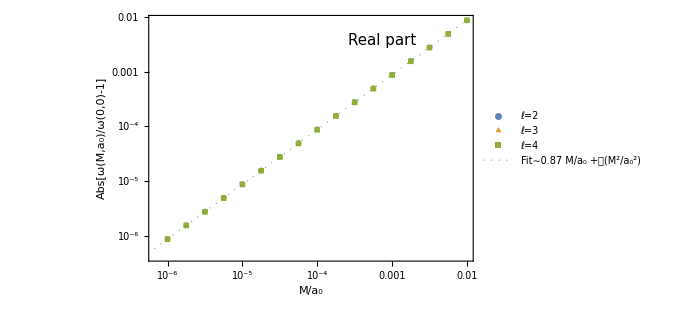

./plot/realZ_H_MM_fit.pdf

```mathematica
Show[p1,LogLogPlot[{ line3R},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]],Directive[Gray,Dotted,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_H_MM_fit.pdf",%]
```

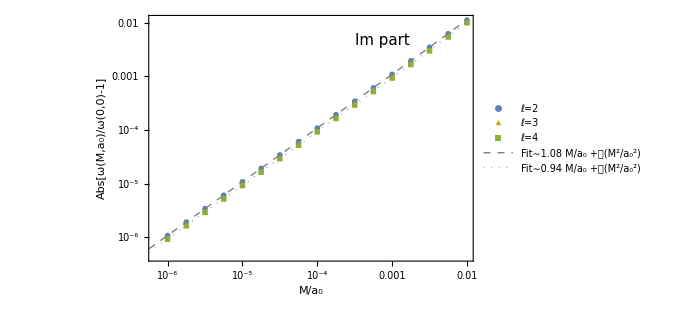

./plot/imZ_H_MM_fit.pdf

```mathematica
Show[p2,LogLogPlot[{line2I, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed, AbsoluteThickness[1]],Directive[Gray,Dotted, AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼1.08 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_H_MM_fit.pdf",%]
```

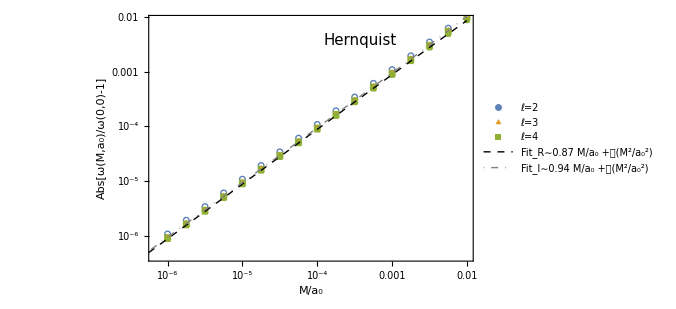

./plot/allZ_H_MM_fit.pdf

```mathematica
p1V=ListLogLogPlot[{
datasetR[l2n0T,10^-2],
datasetR[l3n0T,10^-2],
datasetR[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Hernquist",15,0,0.65,0.9,Black]}];
p2V=ListLogLogPlot[{
datasetI[l2n0T,10^-2],
datasetI[l3n0T,10^-2],
datasetI[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotMarkers->{{○,Large},{△,Medium},{□,Small}}];
Show[p1V,p2V,LogLogPlot[{line2R, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/allZ_H_MM_fit.pdf",%]
```

#### first overtone

```mathematica
l2n1Vac=δω[0,2,1000,SetPrecision[0.35-0.27I,50]];
```

```mathematica
l3n1Vac=δω[0,3,1000,SetPrecision[0.58-0.28I,50]];
```

```mathematica
l4n1Vac=δω[0,4,1000,SetPrecision[0.80-0.28I,50]];
```

```mathematica
l2n1=Monitor[Table[δω[10^compactness[[ii]],2,1000,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n1=Monitor[Table[δω[10^compactness[[ii]],3,1000,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n1=Monitor[Table[δω[10^compactness[[ii]],4,1000,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n1T=Join[{l2n1Vac},l2n1];
l3n1T=Join[{l3n1Vac},l3n1];
l4n1T=Join[{l4n1Vac},l4n1];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2n1R=Fit[datasetR[l2n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line3n1R=Fit[datasetR[l3n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line4n1R=Fit[datasetR[l4n1T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-1.30390667390648150693184682786952575223531357×10^-10+1.67123127745852185046789263683076003728672445 t+58.6290658175532229912555970600814833615715766 t^2

-8.5369245068313919571401834662680251540710332×10^-13+0.46635470082209604846175398638082022691547587 t+62.418125479292264307703917371355028337417878 t^2

4.1002397543812241337142053263839214099030665×10^-11+0.56693370736211369685068523448886426043165445 t+21.280143815499781837943218354815144457287763 t^2

```mathematica
line2n1I=Fit[datasetI[l2n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line3n1I=Fit[datasetI[l3n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line4n1I=Fit[datasetI[l4n1T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-3.10113972894209430289197853592272878579728621×10^-11+0.762594298742088562098331626177789385156099735 t-144.861921059794339029941652442624967806521593 t^2

-1.43138423948222410075733713732388324350642×10^-10+0.0100226739599485977739335807729343200344601 t+38.6625367378560155954794545182101583014576 t^2

1.25975555687668586267154181555890431916540912×10^-10+0.800249035208988107909522317404595690813939773 t-103.468312745671305319196350544326098026506712 t^2

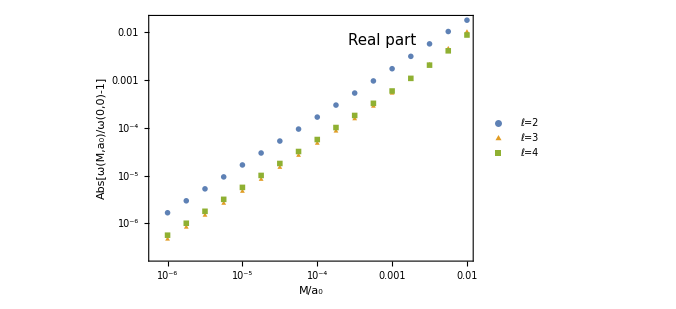

./plot/realZ_H_MM_ov.pdf

```mathematica
pn1=ListLogLogPlot[{
datasetR[l2n1T,10^-2],
datasetR[l3n1T,10^-2],
datasetR[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.72,0.9,Black]}]
Export["./plot/realZ_H_MM_ov.pdf",%]
```

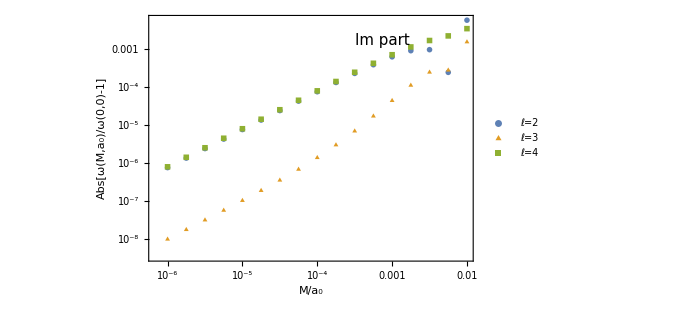

./plot/imZ_H_MM_ov.pdf

```mathematica
pn2=ListLogLogPlot[{
datasetI[l2n1T,10^-2],
datasetI[l3n1T,10^-2],
datasetI[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.72,0.9,Black]}]
Export["./plot/imZ_H_MM_ov.pdf",%]
```

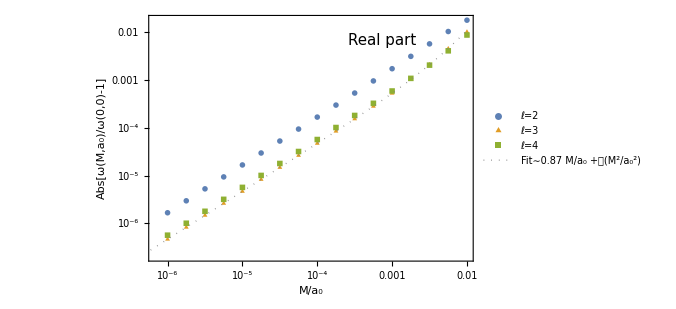

./plot/realZ_H_MM_fit_ov.pdf

```mathematica
Show[pn1,LogLogPlot[{ line3n1R},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]],Directive[Gray,Dotted,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_H_MM_fit_ov.pdf",%]
```

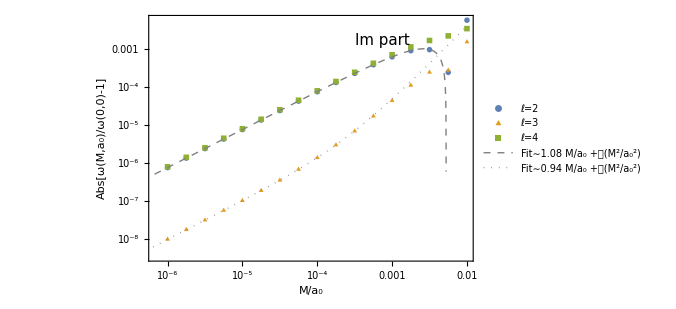

./plot/imZ_H_MM_fit_ov.pdf

```mathematica
Show[pn2,LogLogPlot[{line2n1I, line3n1I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed, AbsoluteThickness[1]],Directive[Gray,Dotted, AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼1.08 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_H_MM_fit_ov.pdf",%]
```

```mathematica
p1V=ListLogLogPlot[{
datasetR[l2n1T,10^-2],
datasetR[l3n1T,10^-2],
datasetR[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Hernquist",15,0,0.65,0.9,Black]}];
p2V=ListLogLogPlot[{
datasetI[l2n1T,10^-2],
datasetI[l3n1T,10^-2],
datasetI[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotMarkers->{{○,Large},{△,Medium},{□,Small}}];
Show[p1V,p2V,LogLogPlot[{line2R, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/allZ_H_MM_fit.pdf",%]
```

-Graphics-

./plot/allZ_H_MM_fit.pdf

#### Export

```mathematica
Export["Matrix_Hern.m",{l2n0T,l3n0T, l4n0T,l2n1T,l3n1T, l4n1T}]
```

Matrix_Hern.m

## Finding modes (2)

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;

ρmetric=background["HQ",M,a0,10^5][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=f'[rh];
derrmh=(D[ρprofile[r,M,a0,"HQ"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37367-0.08897056I,50];*)
FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];


sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

#### fundamental

```mathematica
l2n0Vac=δω[0,2,20,SetPrecision[0.37-0.08I,50]];
```

```mathematica
l3n0Vac=δω[0,3,20,SetPrecision[0.59-0.09I,50]];
```

```mathematica
l4n0Vac=δω[0,4,20,SetPrecision[0.81-0.09I,50]];
```

```mathematica
l2n0=Monitor[Table[δω[10^compactness[[ii]],2,20,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n0=Monitor[Table[δω[10^compactness[[ii]],3,20,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n0=Monitor[Table[δω[10^compactness[[ii]],4,20,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n0T=Join[{l2n0Vac},l2n0];
l3n0T=Join[{l3n0Vac},l3n0];
l4n0T=Join[{l4n0Vac},l4n0];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2R=Fit[datasetR[l2n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line3R=Fit[datasetR[l3n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line4R=Fit[datasetR[l4n0T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-5.8854761923652275378903585012070353671246102×10^-13+0.892535056034730804634065745891153727271085888 t-2.87586059681320725772044132245758330267343499 t^2

-2.3415135905529888271412951774644170122984052×10^-12+0.88137474982197990490227648866927701710637682 t+0.30399435379560894335139995984680104573184478 t^2

-1.43243658162052955868785132305612814743918804×10^-12+0.871447518582611679303401210184814996270844007 t+0.872065802227674835451611002975953768346780389 t^2

```mathematica
line2I=Fit[datasetI[l2n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line3I=Fit[datasetI[l3n0T,10^-4][[2;;-1]],{1,t,t^2},t]
line4I=Fit[datasetI[l4n0T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-1.02345883632816681300164638133762987371277824×10^-11+1.10435964288194068591151869360347828993391227 t+7.10263444714026659395317924095492257299394272 t^2

5.145242072497785639572399998835840721923822×10^-13+0.93131582492649274196255463212214738828927524 t+12.3255412460861378867446215200098431563415 t^2

1.20231610846958815309538536090819152138380441×10^-11+0.911957000197864435282055135641774443072860149 t+6.80313636848082656184253131448629435195801054 t^2

```mathematica
p1=ListLogLogPlot[{
datasetR[l2n0T,10^-2],
datasetR[l3n0T,10^-2],
datasetR[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.72,0.9,Black]}]
Export["./plot/realZ_H_MM.pdf",%]
```

-Graphics-

./plot/realZ_H_MM.pdf

```mathematica
p2=ListLogLogPlot[{
datasetI[l2n0T,10^-2],
datasetI[l3n0T,10^-2],
datasetI[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.72,0.9,Black]}]
Export["./plot/imZ_H_MM.pdf",%]
```

-Graphics-

./plot/imZ_H_MM.pdf

```mathematica
Show[p1,LogLogPlot[{ line3R},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]],Directive[Gray,Dotted,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_H_MM_fit.pdf",%]
```

-Graphics-

./plot/realZ_H_MM_fit.pdf

```mathematica
Show[p2,LogLogPlot[{line2I, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed, AbsoluteThickness[1]],Directive[Gray,Dotted, AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼1.08 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_H_MM_fit.pdf",%]
```

-Graphics-

./plot/imZ_H_MM_fit.pdf

```mathematica
p1V=ListLogLogPlot[{
datasetR[l2n0T,10^-2],
datasetR[l3n0T,10^-2],
datasetR[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Hernquist",15,0,0.65,0.9,Black]}];
p2V=ListLogLogPlot[{
datasetI[l2n0T,10^-2],
datasetI[l3n0T,10^-2],
datasetI[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotMarkers->{{○,Large},{△,Medium},{□,Small}}];
Show[p1V,p2V,LogLogPlot[{line2R, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/allZ_H_MM_fit.pdf",%]
```

-Graphics-

./plot/allZ_H_MM_fit.pdf

#### first overtone

```mathematica
l2n1Vac=δω[0,2,20,SetPrecision[0.35-0.27I,50]];
```

```mathematica
l3n1Vac=δω[0,3,20,SetPrecision[0.58-0.28I,50]];
```

```mathematica
l4n1Vac=δω[0,4,20,SetPrecision[0.80-0.28I,50]];
```

```mathematica
l2n1=Monitor[Table[δω[10^compactness[[ii]],2,20,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n1=Monitor[Table[δω[10^compactness[[ii]],3,20,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n1=Monitor[Table[δω[10^compactness[[ii]],4,20,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n1T=Join[{l2n1Vac},l2n1];
l3n1T=Join[{l3n1Vac},l3n1];
l4n1T=Join[{l4n1Vac},l4n1];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2n1R=Fit[datasetR[l2n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line3n1R=Fit[datasetR[l3n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line4n1R=Fit[datasetR[l4n1T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-1.30390667390648150693184682786952575223531357×10^-10+1.67123127745852185046789263683076003728672445 t+58.6290658175532229912555970600814833615715766 t^2

-8.5369245068313919571401834662680251540710332×10^-13+0.46635470082209604846175398638082022691547587 t+62.418125479292264307703917371355028337417878 t^2

4.1002397543812241337142053263839214099030665×10^-11+0.56693370736211369685068523448886426043165445 t+21.280143815499781837943218354815144457287763 t^2

```mathematica
line2n1I=Fit[datasetI[l2n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line3n1I=Fit[datasetI[l3n1T,10^-4][[2;;-1]],{1,t,t^2},t]
line4n1I=Fit[datasetI[l4n1T,10^-4][[2;;-1]],{1,t,t^2},t]
```

-3.10113972894209430289197853592272878579728621×10^-11+0.762594298742088562098331626177789385156099735 t-144.861921059794339029941652442624967806521593 t^2

-1.43138423948222410075733713732388324350642×10^-10+0.0100226739599485977739335807729343200344601 t+38.6625367378560155954794545182101583014576 t^2

1.25975555687668586267154181555890431916540912×10^-10+0.800249035208988107909522317404595690813939773 t-103.468312745671305319196350544326098026506712 t^2

```mathematica
pn1=ListLogLogPlot[{
datasetR[l2n1T,10^-2],
datasetR[l3n1T,10^-2],
datasetR[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.72,0.9,Black]}]
Export["./plot/realZ_H_MM_ov.pdf",%]
```

-Graphics-

./plot/realZ_H_MM_ov.pdf

```mathematica
pn2=ListLogLogPlot[{
datasetI[l2n1T,10^-2],
datasetI[l3n1T,10^-2],
datasetI[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.72,0.9,Black]}]
Export["./plot/imZ_H_MM_ov.pdf",%]
```

-Graphics-

./plot/imZ_H_MM_ov.pdf

```mathematica
Show[pn1,LogLogPlot[{ line3n1R},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]],Directive[Gray,Dotted,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_H_MM_fit_ov.pdf",%]
```

-Graphics-

./plot/realZ_H_MM_fit_ov.pdf

```mathematica
Show[pn2,LogLogPlot[{line2n1I, line3n1I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed, AbsoluteThickness[1]],Directive[Gray,Dotted, AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼1.08 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_H_MM_fit_ov.pdf",%]
```

-Graphics-

./plot/imZ_H_MM_fit_ov.pdf

```mathematica
p1V=ListLogLogPlot[{
datasetR[l2n1T,10^-2],
datasetR[l3n1T,10^-2],
datasetR[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Hernquist",15,0,0.65,0.9,Black]}];
p2V=ListLogLogPlot[{
datasetI[l2n1T,10^-2],
datasetI[l3n1T,10^-2],
datasetI[l4n1T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotMarkers->{{○,Large},{△,Medium},{□,Small}}];
Show[p1V,p2V,LogLogPlot[{line2R, line3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.87 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.94 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/allZ_H_MM_fit.pdf",%]
```

-Graphics-

./plot/allZ_H_MM_fit.pdf

#### Export

```mathematica
Export["Matrix_Hern.m",{l2n0T,l3n0T, l4n0T,l2n1T,l3n1T, l4n1T}]
```

Matrix_Hern.m